```mathematica
MobiusMatrix[allGraphs2]//MatrixForm
```

(1 | -1
0 | 1)

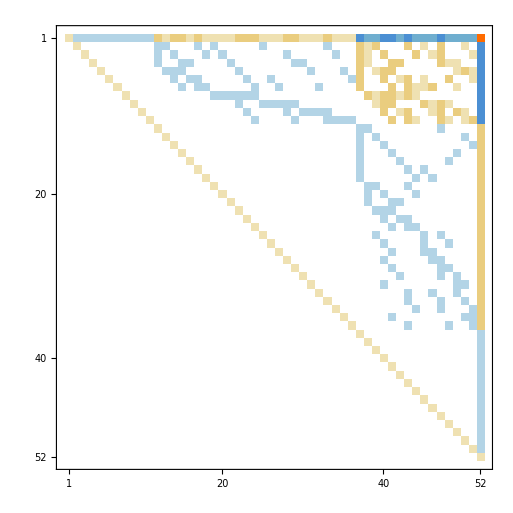

```mathematica
MobiusMatrix[allGraphs5]//MatrixPlot
```

```mathematica
Banded[vect_,n_]:=Table[
Table[
j
,{j,{StirlingS2[n,i],StirlingS2[n,i+1]}}]
,{i,1,n}]
```

```mathematica
Banded[Table[Indexed[x,i],{i,1,15}],4]
```

{{1,7},{7,6},{6,1},{1,0}}

```mathematica
allGraphs4NullAtomKeysSorted=Sort[allGraphs4NullAtomKeys,CompareSymbols[allGraphs[#1,"colofourrealnull"],allGraphs[#2,"colofourrealnull"]]&]
```

{0,2,18,6,486,162,54,26,488,666,546,168,218,72,728}

```mathematica
Table[Indexed[x,allGraphs4[k,"vertexsets"]],{k,allGraphs4NullAtomKeysSorted}]
```

{x{1}{2}{3}{4},x{1}{2}{3,4},x{1}{2,3}{4},x{1}{2,4}{3},x{1,2}{3}{4},x{1,3}{2}{4},x{1,4}{2}{3},x{1}{2,3,4},x{1,2}{3,4},x{1,2,3}{4},x{1,2,4}{3},x{1,3}{2,4},x{1,3,4}{2},x{1,4}{2,3},x{1,2,3,4}}

```mathematica
Table[Indexed[x,allGraphs4[k,"vertexsets"]],{k,allGraphs4NullAtomKeysSorted}].Inverse[MobiusMatrix[allGraphs4]]//MatrixForm
```

(x{1}{2}{3}{4}
x{1}{2}{3,4}+x{1}{2}{3}{4}
x{1}{2,3}{4}+x{1}{2}{3}{4}
x{1}{2,4}{3}+x{1}{2}{3}{4}
x{1,2}{3}{4}+x{1}{2}{3}{4}
x{1,3}{2}{4}+x{1}{2}{3}{4}
x{1,4}{2}{3}+x{1}{2}{3}{4}
x{1}{2,3,4}+x{1}{2}{3,4}+x{1}{2,3}{4}+x{1}{2,4}{3}+x{1}{2}{3}{4}
x{1,2}{3,4}+x{1}{2}{3,4}+x{1,2}{3}{4}+x{1}{2}{3}{4}
x{1,2,3}{4}+x{1}{2,3}{4}+x{1,2}{3}{4}+x{1,3}{2}{4}+x{1}{2}{3}{4}
x{1,2,4}{3}+x{1}{2,4}{3}+x{1,2}{3}{4}+x{1,4}{2}{3}+x{1}{2}{3}{4}
x{1,3}{2,4}+x{1}{2,4}{3}+x{1,3}{2}{4}+x{1}{2}{3}{4}
x{1,3,4}{2}+x{1}{2}{3,4}+x{1,3}{2}{4}+x{1,4}{2}{3}+x{1}{2}{3}{4}
x{1,4}{2,3}+x{1}{2,3}{4}+x{1,4}{2}{3}+x{1}{2}{3}{4}
x{1,2,3,4}+x{1}{2,3,4}+x{1,2}{3,4}+x{1,3}{2,4}+x{1,4}{2,3}+x{1,2,3}{4}+x{1,2,4}{3}+x{1,3,4}{2}+x{1}{2}{3,4}+x{1}{2,3}{4}+x{1}{2,4}{3}+x{1,2}{3}{4}+x{1,3}{2}{4}+x{1,4}{2}{3}+x{1}{2}{3}{4})

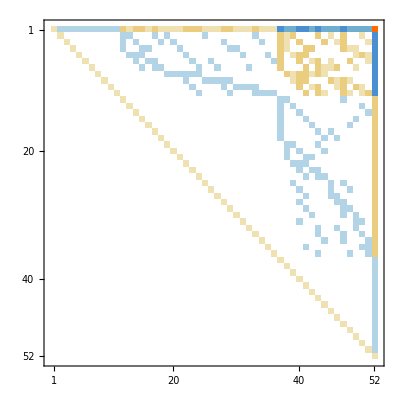

```mathematica
Mobius5=MobiusMatrix[allGraphs5];MatrixPlot[Mobius5]
```

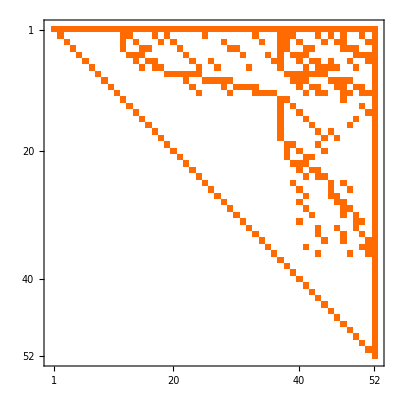

```mathematica
Zeta5=Inverse[Mobius5];MatrixPlot[Zeta5]
```

```mathematica
Map[Length[Select[#,#≠0&]]&,Zeta5]
```

{52,15,15,15,15,15,15,15,15,15,15,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1}

```mathematica
Map[Length[Select[#,#≠0&]]&,Transpose[Zeta5]]
```

{1,2,2,2,2,2,2,2,2,2,2,5,4,5,5,4,5,4,4,4,4,5,5,5,4,4,4,5,5,4,4,4,5,4,4,4,15,10,10,15,15,10,15,10,10,10,15,10,10,10,10,52}

```mathematica
Map[Length[ListofVars[#]]&,Table[Indexed[x,i],{i,1,52}].Zeta5]//MatrixForm
```

(1
2
2
2
2
2
2
2
2
2
2
5
4
5
5
4
5
4
4
4
4
5
5
5
4
4
4
5
5
4
4
4
5
4
4
4
15
10
10
15
15
10
15
10
10
10
15
10
10
10
10
52)

```mathematica
TableForm[First[Solve[ Table[Indexed[x,i],{i,1,52}].Inverse[Mobius5]==Table[If[i<2,1,0],{i,1,52}]]],TableDirections->Column]
```

x1→1
x2→-1
x3→-1
x4→-1
x5→-1
x6→-1
x7→-1
x8→-1
x9→-1
x10→-1
x11→-1
x12→2
x13→1
x14→2
x15→2
x16→1
x17→2
x18→1
x19→1
x20→1
x21→1
x22→2
x23→2
x24→2
x25→1
x26→1
x27→1
x28→2
x29→2
x30→1
x31→1
x32→1
x33→2
x34→1
x35→1
x36→1
x37→-6
x38→-2
x39→-2
x40→-6
x41→-6
x42→-2
x43→-6
x44→-2
x45→-2
x46→-2
x47→-6
x48→-2
x49→-2
x50→-2
x51→-2
x52→24

```mathematica
Table[StirlingS2[5,k],{k,1,5}]
```

{1,15,25,10,1}

```mathematica
Map[#[[2]]≥0&,First[Solve[ Table[Indexed[x,i],{i,1,52}].Zeta5==Table[If[i<17,Indexed[a,i],0],{i,1,52}]]]]//Simplify
```

{a1≥0,a2≥a1,a3≥a1,a4≥a1,a5≥a1,a6≥a1,a7≥a1,a8≥a1,a9≥a1,a10≥a1,a11≥a1,2 a1+a12≥a2+a3+a4,a1+a13≥a2+a5,2 a1+a14≥a3+a5+a6,2 a1+a15≥a4+a5+a7,a1+a16≥a4+a6,2 a1≥a2+a6+a7,a1≥a3+a7,a1≥a2+a8,a1≥a3+a8,a1≥a4+a8,2 a1≥a5+a8+a9,2 a1≥a6+a8+a10,2 a1≥a7+a8+a11,a1≥a2+a9,a1≥a6+a9,a1≥a7+a9,2 a1≥a3+a9+a10,2 a1≥a4+a9+a11,a1≥a4+a10,a1≥a5+a10,a1≥a7+a10,2 a1≥a2+a10+a11,a1≥a3+a11,a1≥a5+a11,a1≥a6+a11,2 (a2+a3+a4+a5+a6+a7)≥6 a1+a12+a13+a14+a15+a16,a2+a3+a4+2 a8≥2 a1+a12,2 a2+a5+a8+a9≥2 a1+a13,2 (a3+a5+a6+a8+a9+a10)≥6 a1+a14,2 (a4+a5+a7+a8+a9+a11)≥6 a1+a15,2 a4+a6+a8+a10≥2 a1+a16,a2+a6+a7+a8+a10+a11≥3 a1,2 a3+a7+a8+a11≥2 a1,a2+a6+a7+2 a9≥2 a1,a3+2 a7+a9+a10≥2 a1,2 (a2+a3+a4+a9+a10+a11)≥6 a1+a12,a4+2 a6+a9+a11≥2 a1+a16,a4+a5+a7+2 a10≥2 a1+a15,a2+2 a5+a10+a11≥2 a1+a13,a3+a5+a6+2 a11≥2 a1+a14,12 a1+a12+a13+a14+a15+a16≥3 (a2+a3+a4+a5+a6+a7+a8+a9+a10+a11)}

```mathematica
Length[allGraphs6]
```

53071

```mathematica
Keys[allGraphs6[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofourrealnull}

```mathematica
Select[Keys[allGraphs6],KeyExistsQ[allGraphs6[#],"colofour"]&]//Length
```

53071

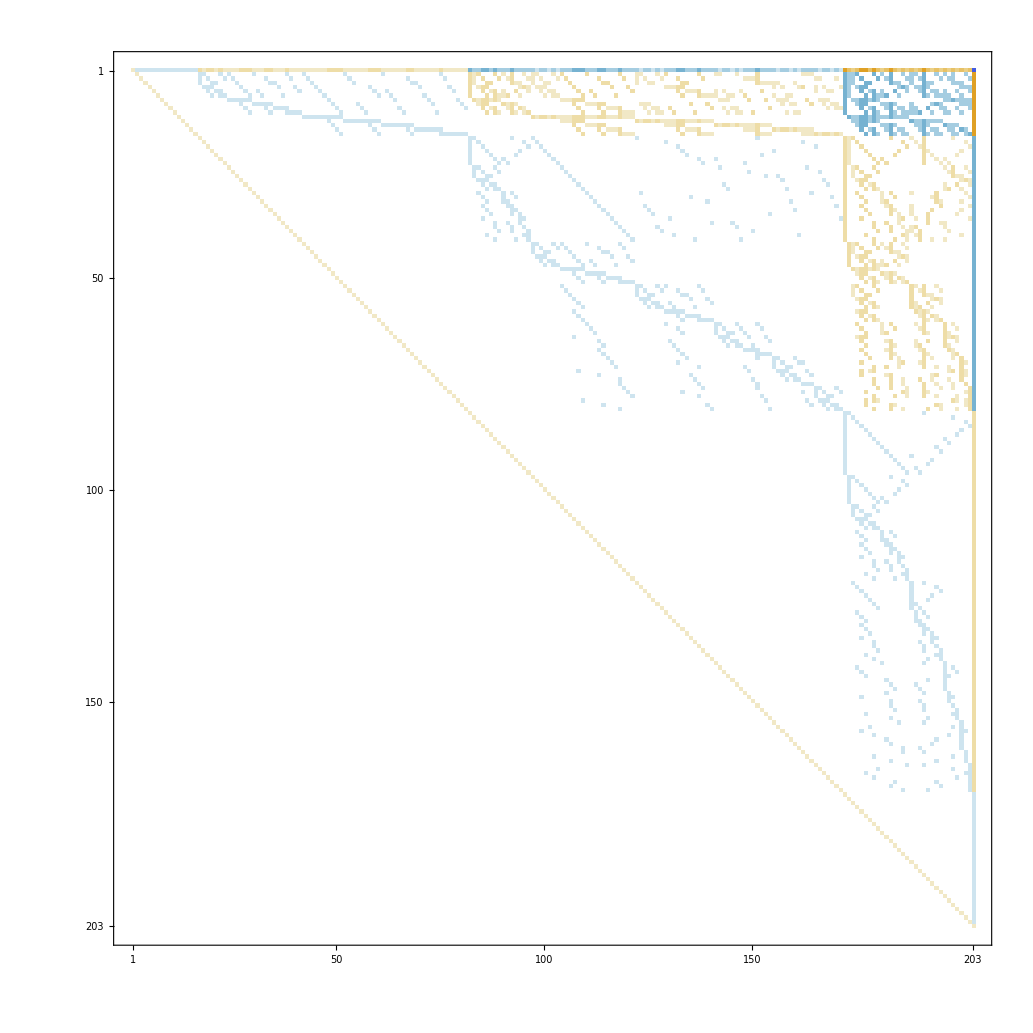

```mathematica
Mobius6=MobiusMatrix[allGraphs6];MatrixPlot[Mobius6]
```

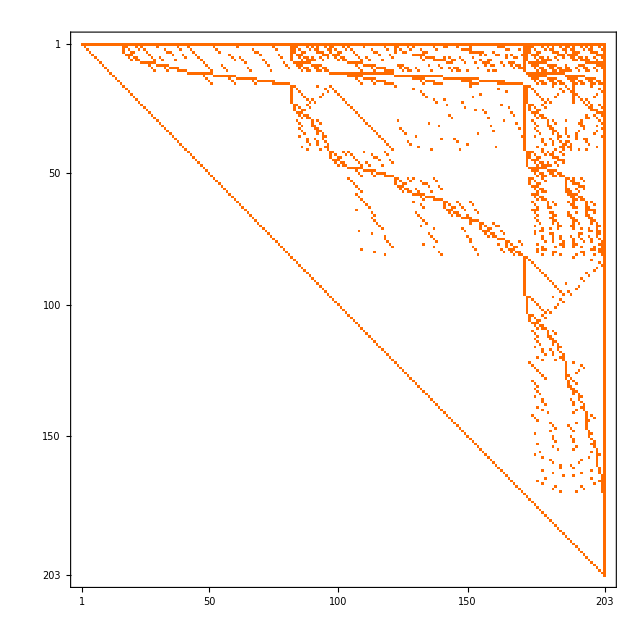

```mathematica
Zeta6=Inverse[Mobius6];Zeta6//MatrixPlot
```